```mathematica
(*HNL DECAYS TOO MESONS/LEPTONS*)(*ESTE SCRIPT GENERA LOS ARCHIVOS PCONFIG QUE UTILIZA PYTHIA8.*)(*NOTAR QUE SIEMPRE TOMA COMO ARGUMENTO LA MASA DEL HNL*)e=.5*10^-3;mu=0.1056583;tau=1.776;leptons={e,mu,tau};
tfactor=1.5193*10^24; (* para pasar de s a GeV^-1 *)
mmc=3*10^11;(*para pasar de s a mm/c*);
ckm=({{0.9742,0.2243,0.0365},{0.218,0.997,0.0422},{0.0081,0.0394,1.019}});
gf=1.166378*10^-5;
xw=0.2223;
gll=-(1/2)+xw;
glr=xw;

(* charged tau *)
tau15 = {290.3*10^-15*tfactor,1.77686,Null,Null,15};

(*charged pseudoscalar*)
d431={504*10^-15*tfactor,1.96834,249.0*10^-3,ckm[[2,2]],431};
d431bar={504*10^-15*tfactor,1.96834,249.0*10^-3,ckm[[2,2]],-431};
d411={1040*10^-15*tfactor,1.86958,211.9*10^-3,ckm[[2,1]],411};
d411bar={1040*10^-15*tfactor,1.86958,211.9*10^-3,ckm[[2,1]],-411};
k321={1.238*10^-8*tfactor,493.677*10^-3,155.6*10^-3,ckm[[1,2]]};
pi211={2.6*10^-8*tfactor,139.57061*10^-3,130.2*10^-3,ckm[[1,1]]};

(*Charged vector*)
k323={Null,895.55*10^-3,0.1827,ckm[[1,2]]};(*K*(892)*)
rho770c={Null,775.26*10^-3,0.162,ckm[[1,1]]};

(*neutral pseudoscalar*)
pi111={Null,134.977*10^-3,130.2*10^-3,Null};
eta221={Null,547.862*10^-3,81.7*10^-3,Null};(*eta*)eta331={Null,957.78*10^-3,-94.7*10^-3,Null};(*eta'(958)*)(*Neutral vector*)rho770n={Null,775.26*10^-3,0.162,1-2xw};
omega782={Null,782.65*10^-3,0.153,4/3 xw};
phi1020={Null,1.019461,0.234,4/3 xw-1};
```

## extras

```mathematica
tauwidth0=1/(290.3*10^-15*tfactor);
lambda[a_,b_,c_]:=a^2+b^2+c^2-2a*b-2b*c-2c*a;
```

## Widths

```mathematica
(* tau > HNL P  - Shaposhnikov *)
(* u siempre es utau *)
tauwidth01[meson_,n_,u_]:=
Re[u^2/(16Pi)gf^2*meson[[4]]^2*meson[[3]]^2*tau15[[2]]^2*((1-n^2/tau15[[2]]^2)^2-meson[[2]]^2/tau15[[2]]^2(1+n^2/tau15[[2]]^2))*√((1-(meson[[2]]^2-n^2)/tau15[[2]]^2)(1-(meson[[2]]^2+n^2)/tau15[[2]]^2))*UnitStep[tau15[[2]]-n-meson[[2]]]];
```

```mathematica
(* tau > HNL V - Shaposhnikov *)
(* u siempre es utau *)
tauwidth02[meson_,n_,u_]:=
Re[u^2/(16Pi)gf^2*meson[[4]]^2*meson[[3]]^2*tau15[[2]]^2*((1-n^2/tau15[[2]]^2)^2-meson[[2]]^2/tau15[[2]]^2(1+n^2/tau15[[2]]^2-2*meson[[2]]^2/tau15[[2]]^2))*√((1-(meson[[2]]^2-n^2)/tau15[[2]]^2)(1-(meson[[2]]^2+n^2)/tau15[[2]]^2))*UnitStep[tau15[[2]]-n-meson[[2]]]];
```

```mathematica
(* tau > HNL l1 nubar1 - Bondarenko 2.8 *)
(* u SIEMPRE es utau *)
tauwidth03[n_,l_,u_]:=Re[(gf^2 tau15[[2]]^5)/(96 Pi^3)u^2*NIntegrate[1/z^3(z-(l/tau15[[2]])^2)^2 √lambda[1,z,(n/tau15[[2]])^2]*((z+2(l/tau15[[2]])^2)(1-(n/tau15[[2]])^2)^2+z(z-(l/tau15[[2]])^2)(1+(n/tau15[[2]])^2-(l/tau15[[2]])^2)-z(l/tau15[[2]])^4-2 z^3),{z,(l/tau15[[2]])^2,(1-(n/tau15[[2]]))^2}]*UnitStep[tau15[[2]]-n-l]];
```

```mathematica
(* tau > nutau l1 HNL - Bondarenko 2.8 *)
(* u puede ser de cualquier sabor *)
tauwidth04[l_,n_,u_]:=Re[(gf^2 tau15[[2]]^5)/(96 Pi^3)u^2*NIntegrate[1/z^3(1-z)^2 √lambda[z,(n/tau15[[2]])^2,(l/tau15[[2]])^2]*(2 z^3+z-z(1-z)(1-(n/tau15[[2]])^2-(l/tau15[[2]])^2)-(2+z)((n/tau15[[2]])^2-(l/tau15[[2]])^2)^2),{z,(l/tau15[[2]]+n/tau15[[2]])^2,1}]*UnitStep[tau15[[2]]-l-n]];
```

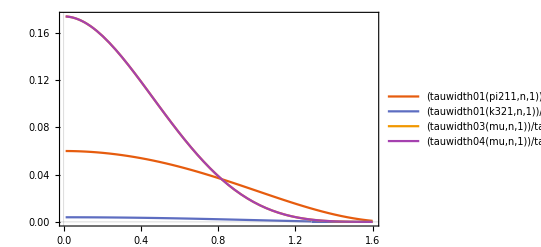

```mathematica
Plot[{tauwidth01[pi211,n,1]/tauwidth0,tauwidth01[k321,n,1]/tauwidth0,tauwidth03[mu,n,1]/tauwidth0,tauwidth04[mu,n,1]/tauwidth0},{n,0.01,0.9tau15[[2]]},PlotRange->All,PlotTheme->"Scientific",PlotLegends->"Expressions"]
```

## Dirac

```mathematica
(* u siempre es utau *)
tau2PiN[n_,mixtau_]:=tauwidth01[pi211,n,mixtau];
tau2KN[n_,mixtau_]:=tauwidth01[k321,n,mixtau];
tau2KstarN[n_,mixtau_]:=tauwidth02[k323,n,mixtau];
tau2rhocN[n_,mixtau_]:=tauwidth02[rho770c,n,mixtau];
tau2Nenue[n_,mixtau_]:=tauwidth03[n,e,mixtau];
tau2Nmunumu[n_,mixtau_]:=tauwidth03[n,mu,mixtau];
(* u puede ser cualquiera *)
tau2nutaueN[n_,mixe_]:=tauwidth04[e,n,mixe];
tau2nutaumuN[n_,mixmu_]:=tauwidth04[mu,n,mixmu];
```

```mathematica
tautotalw[n_,mixe_,mixmu_,mixtau_]:=
Re[1/tau15[[1]]
+tau2PiN[n,mixtau]+tau2KN[n,mixtau]
+tau2KstarN[n,mixtau]+tau2rhocN[n,mixtau]
+tau2Nenue[n,mixtau]+tau2Nmunumu[n,mixtau]
+tau2nutaueN[n,mixe]+tau2nutaumuN[n,mixmu]];
```

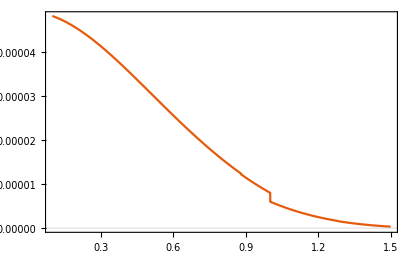

```mathematica
(* Aproximación estimada de la relación HNLwidths/totalw *)
Plot[{(tau2PiN[n,10^-2]+tau2KN[n,10^-2]
+tau2KstarN[n,10^-2]+tau2rhocN[n,10^-2]
+tau2Nenue[n,10^-2]+tau2Nmunumu[n,10^-2]
+tau2nutaueN[n,10^-3]+tau2nutaumuN[n,10^-3])/tautotalw[n,10^-3,10^-3,10^-2]},{n,0.1,1.5},PlotTheme->"Scientific"]
```

```mathematica
(* tau param *)
tauparam[n_,mixe_,mixmu_,mixtau_]:=
{"15:mayDecay = true",
"15:tau0 = "<>ToString[AccountingForm[Re[1/tautotalw[n,mixe,mixmu,mixtau]]*1/tfactor*mmc,16]],
"15:m0 = "<>ToString[AccountingForm[tau15[[2]],16]]};
```

```mathematica
(* tau BRs *)
expbrtau[n_,mixe_,mixmu_,mixtau_]:={
(*(1)-6 canales*)
"15:oneChannel = 1 "<>ToString[AccountingForm[tau2PiN[n,mixtau]/tautotalw[n,mixe,mixmu,mixtau],16]]<>" 1521 2000000001 -211",
"15:addChannel = 1 "<>ToString[AccountingForm[tau2KN[n,mixtau]/tautotalw[n,mixe,mixmu,mixtau],16]]<>" 1521 2000000001 -321",
"15:addChannel = 1 "<>ToString[AccountingForm[tau2KstarN[n,mixtau]/tautotalw[n,mixe,mixmu,mixtau],16]]<>" 1521 2000000001 -323",
"15:addChannel = 1 "<>ToString[AccountingForm[tau2rhocN[n,mixtau]/tautotalw[n,mixe,mixmu,mixtau],16]]<>" 1521 2000000001 -213",
"15:addChannel = 1 "<>ToString[AccountingForm[tau2Nenue[n,mixtau]/tautotalw[n,mixe,mixmu,mixtau],16]]<>" 1531 2000000001 11 -12",
"15:addChannel = 1 "<>ToString[AccountingForm[tau2Nmunumu[n,mixtau]/tautotalw[n,mixe,mixmu,mixtau],16]]<>" 1531 2000000001 13 -14",
"15:addChannel = 1 "<>ToString[AccountingForm[tau2nutaueN[n,mixe]/tautotalw[n,mixe,mixmu,mixtau],16]]<>" 1531 16 11 -2000000001",
"15:addChannel = 1 "<>ToString[AccountingForm[tau2nutaumuN[n,mixmu]/tautotalw[n,mixe,mixmu,mixtau],16]]<>" 1531 16 13 -2000000001"};
```

```mathematica
(* taubar BRs: NO ES NECESARIO PARA DIRAC, SÍ PARA MAJORANA *)
expbrtaubar[n_,mixe_,mixmu_,mixtau_]:={
(*(1)-6 canales*)
"-15:oneChannel = 1 "<>ToString[AccountingForm[tau2PiN[n,mixtau]/tautotalw[n,mixe,mixmu,mixtau],16]]<>" 1521 -2000000001 211",
"-15:addChannel = 1 "<>ToString[AccountingForm[tau2KN[n,mixtau]/tautotalw[n,mixe,mixmu,mixtau],16]]<>" 1521 -2000000001 321",
"-15:addChannel = 1 "<>ToString[AccountingForm[tau2KstarN[n,mixtau]/tautotalw[n,mixe,mixmu,mixtau],16]]<>" 1521 -2000000001 323",
"-15:addChannel = 1 "<>ToString[AccountingForm[tau2rhocN[n,mixtau]/tautotalw[n,mixe,mixmu,mixtau],16]]<>" 1521 -2000000001 213",
"-15:addChannel = 1 "<>ToString[AccountingForm[tau2Nenue[n,mixtau]/tautotalw[n,mixe,mixmu,mixtau],16]]<>" 1531 -2000000001 -11 12",
"-15:addChannel = 1 "<>ToString[AccountingForm[tau2Nmunumu[n,mixtau]/tautotalw[n,mixe,mixmu,mixtau],16]]<>" 1531 -2000000001 -13 14",
"-15:addChannel = 1 "<>ToString[AccountingForm[tau2nutaueN[n,mixe]/tautotalw[n,mixe,mixmu,mixtau],16]]<>" 1531 -16 -11 2000000001",
"-15:addChannel = 1 "<>ToString[AccountingForm[tau2nutaumuN[n,mixmu]/tautotalw[n,mixe,mixmu,mixtau],16]]<>" 1531 -16 -13 2000000001"};
```

```mathematica
Export[NotebookDirectory[]<>"taubrs.dat",Join[tauparam[1,1,1,1],expbrtau[1,1,1,1],expbrtaubar[1,1,1,1]]]
```

/home/sane/mainhnlchain/taubrs.dat

Falta:
ver cuaderno